```mathematica
SetDirectory[NotebookDirectory[]];
muon=Import["../Data/muon.csv", {"Data", All,Range[1,6]}];(*event no., momentum in ID, track in muon detector, difference, eta, phi*)
electron = Import["../Data/electron.csv", {"Data",All,Range[1,4]}];(*event no., momentum in inner detector, energy ECAL, E/p*)
```

```mathematica
muonEnergyLoss = Map[#[[4]]&,muon]
onlyPositiveEnergyLoss = Select[muonEnergyLoss, #>0&]
averageEnergyLoss = Mean[muonEnergyLoss]
averageFilteredEnergyLoss = Mean[onlyPositiveEnergyLoss]
```

{31.36,-0.43,4.35,4.12,-9.46,20.76,6.98,0.47,7.83,71.1,6.64,3.78,-3.49,-27.49,6.18,-5.45,3.05,4.19,16.66,-3.72}

{31.36,4.35,4.12,20.76,6.98,0.47,7.83,71.1,6.64,3.78,6.18,3.05,4.19,16.66}

6.8715

13.3907

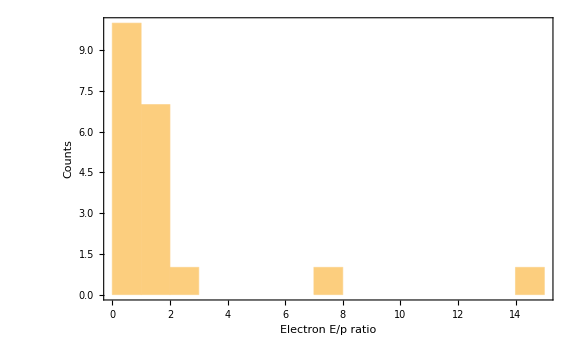

```mathematica
Histogram[Map[#[[4]]&,electron],15, PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{Style["Electron E/p ratio",Medium],Style["Counts",Medium]},ImageSize -> Large]
```